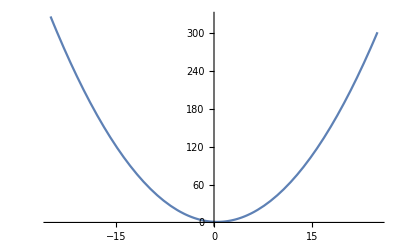

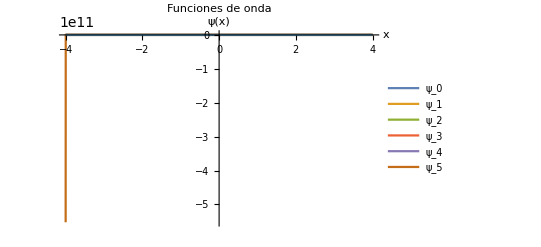

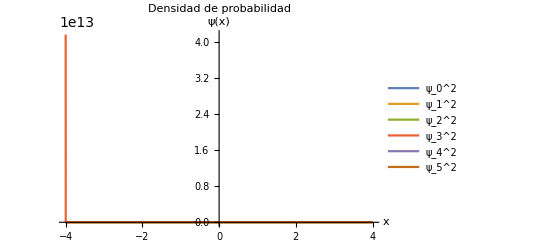

```mathematica
a=1/2;
b=4;
c=4;
m=b*c/((b+x)*(c-x));
h=1;
w=1;
f[x_,a_]:=(1-a)*x^2-(1-a)x+1;
f1[x_,a_]:=Exp[-x^2*(1-a)];
f[x_,a_]:=(Cos[x*(1-a)]+2)/3;
f4[x_,a_]:=(Exp[-x])^(1-a);
f3[x_,a_]:=a^2/(a^2-x^2);
f1[x_,a_,b_]:=a*b/((a+x)*(b-x))
Plot[f[x,a],{x,-25,25},PlotRange->All]
g=Integrate[x*m/f[x,a],x];
Psi0:=Exp[-w/h *g]
Psi1=(1/Sqrt[1!])*(m*w*x*Psi0-h*f[x,a]*D[Psi0,x])/Sqrt[2*m*h*w];
Psi2=(1/Sqrt[2!])*(m*w*x*Psi1-h*f[x,a]*D[Psi1,x])/Sqrt[2*m*h*w];
Psi3=(1/Sqrt[3!])*(m*w*x*Psi2-h*f[x,a]*D[Psi2,x])/Sqrt[2*m*h*w];
Psi4=(1/Sqrt[4!])*(m*w*x*Psi3-h*f[x,a]*D[Psi3,x])/Sqrt[2*m*h*w];
Psi5=(1/Sqrt[5!])*(m*w*x*Psi4-h*f[x,a]*D[Psi4,x])/Sqrt[2*m*h*w];

p2=Plot[{Psi0^2,Psi1^2,Psi2^2,Psi3^2,Psi4^2,Psi5^2},{x,-4,4},PlotRange->All,PlotLegends->{"ψ_0^2","ψ_1^2","ψ_2^2","ψ_3^2","ψ_4^2","ψ_5^2"},PlotLabel->"Densidad de probabilidad",AxesLabel->{"x","ψ(x)"}]
```

```mathematica
]]
```

1/3

2 x

-2 x^(2/3)+4 x^2

(4 x^(1/3))/3-12 x^(5/3)+8 x^3

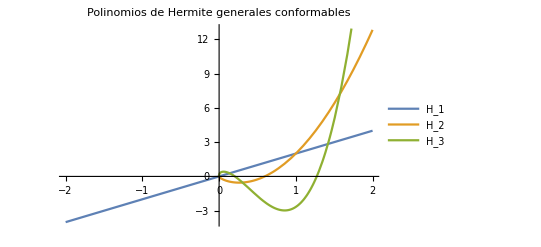

```mathematica
b=1/3
r[x_,b_]:=Exp[(-x^2)(1-b)]
h1=2x
h2=4x^2-2r[x,b]
h3=8x^3-12x*r[x,b]+2r[x,b]*D[r[x,b],x]
Plot[{h1,h2,h3},{x,-2,2},PlotLegends->{"H_1","H_2","H_3"},PlotLabel->"Polinomios de Hermite generales conformables"]
```

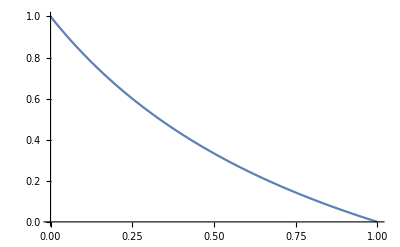

```mathematica
Plot[(1-x)/(1+x),{x,0,1}]
```

```mathematica
a=1/3
```

1/3

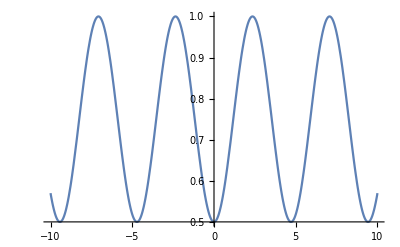

```mathematica
Plot[(3-Cos[2*(1-a)*x])/4,{x,-10,10}]
```